## Functions

```mathematica
SetOptions[$FrontEndSession,AutoStyleOptions->{"SymbolContextStyles"->{"global`"->Purple}}]

AppendTo[$ContextPath,"global`"];
```

```mathematica
UncertaintySum[{a_,σa_},X:{_,_}...]:=Fold[{#1[[1]]+#2[[1]],√((#1[[2]])^2+(#2[[2]])^2)}&,{a,σa},{X}]
```

### Cell["Importing", "Subsection", CellChangeTimes->{{3.690279199275955*^9, 3.690279207508403*^9}}]

```mathematica
BuildFilePath[root_,date_,file_]:=root<>date<>"/"<>file<>"/"<>file<>".txt"
```

```mathematica
ImportDataFile[pathToFile_]:=Module[{nans,rawData},
nans=ConstantArray["nan",4];
rawData=Import[pathToFile,"Data"];
Developer`ToPackedArray/@Round/@Rest/@Most@Split[Prepend[rawData,nans],(#2=!=nans)&]
]
```

```mathematica
ImportDataFiles[pathToFiles_]:=Join@@(ImportDataFile/@pathToFiles)
```

### Cell["Cleaning", "Subsection", CellChangeTimes->{{3.690279199275955*^9, 3.690279242366008*^9}}]

```mathematica
CompensateDetectorLags[data_,lags_,lenStirap_]:=Module[{rules},

rules=Append[Rule@@@lags,_Integer:>0];

Function[{m},
With[{ls=m[[;;,1]]/.rules},
Transpose[{
m[[;;,1]],
Mod[m[[;;,2]]-ls,lenStirap],
m[[;;,3]]-ls,
m[[;;,4]]-UnitStep[ls-m[[;;,2]]]
}]
]
]/@data
]
```

### Cell["Filtering", "Subsection", CellChangeTimes->{{3.690279199275955*^9, 3.690279219310535*^9}}]

```mathematica
(*Choosing to have crit@ rather than crit/@, crit must be Listable?*)
FilterByCriteria[data_,columnSpec_, crit_,results_List]:=Pick[data,crit@data[[;;,;;,columnSpec]],#]&/@results
FilterByCriteria[data_,columnSpec_, crit_,result_]:=Pick[data,crit@data[[;;,;;,columnSpec]],result]

FilterByDetector[data_,detectors_]:=FilterByCriteria[data,1,Identity,detectors]
FilterByPulseParities[data_,parities_List]:=FilterByCriteria[data,4,#,True]&/@parities
FilterByPulseParities[data_,parity_]:=FilterByCriteria[data,4,parity,True]
FilterByPulseRange[data_,{min_,max_}]:=FilterByCriteria[data,4,(UnitStep[#-min]+UnitStep[#-max-1])&,1]
```

### Cell["Statistics", "Subsection", CellChangeTimes->{{3.690279199275955*^9, 3.690279236126224*^9}}]

```mathematica
HomCorrelations[data_,detPairs:{{_Integer,_Integer}..},func_:Subtract]:=Module[{assoc,emptyAssoc,flatRiffledData,ditheredDiffs,homBunches,groupbyInput},

flatRiffledData=Join@@Riffle[DeleteCases[data,{}],{{{-1,-1,-1,-1}}}];
ditheredDiffs=(Prepend[#,1]*Append[#,1])&@Differences[flatRiffledData[[;;,4]]];
homBunches=SplitBy[Pick[flatRiffledData,ditheredDiffs,0],Last];
groupbyInput=Transpose/@Flatten[Subsets[#,{2}]&/@homBunches,1];

assoc=GroupBy[groupbyInput,First->(#[[2]]&)];

emptyAssoc=AssociationThread[#->ConstantArray[{},Length[#]]]&@Union[detPairs,Reverse/@detPairs];
assoc=Merge[{assoc,emptyAssoc},Flatten[#,1]&];

Map[func@@#&,
If[SameQ@@#,assoc[#],Flatten[{assoc[#],Reverse/@assoc[Reverse@#]},1]]&/@detPairs,
{2}
]
]
```

```mathematica
Correlations[data_,det1_,det2_,column_:3]:=
If[det1==det2,
(#[[;;,2]]-#[[;;,1]])&@(Join@@(Subsets[#[[;;,4]],{2}]&/@FilterByDetector[data,det1])),
Flatten[
Outer[Plus,#[[1,;;,column]],-#[[2,;;,column]]]&/@Transpose[FilterByDetector[data,{det1,det2}]]
]
]
```

```mathematica
RealPhotonsPerThrow[data_,atomWindow_,backWindow_]:=Module[{nAtom,nBack,σAtom,σBack,scaleFactor},

nAtom=Length[Flatten[FilterByPulseRange[data,atomWindow],1]];
nBack=Length[Flatten[FilterByPulseRange[data,backWindow],1]];

scaleFactor=(Subtract@@atomWindow)/(Subtract@@backWindow);

σAtom=√nAtom;
σBack=√nBack;

{nAtom,σAtom}={nAtom,σAtom}/Length[data];
{nBack,σBack}=scaleFactor{nBack,σBack}/Length[data];

N@{{nAtom-nBack,√(σAtom^2+σBack^2)},{nBack,σBack}}

]
```

```mathematica
NCorrelationsPerThrow[data_,detectors_List,idx_List,idxBack_List:Range[101,200]]:=Module[{correls,countsDet1,countsDet2,backCorrels},

{correls,backCorrels}=Transpose[
Table[
Total/@{#[[idx]],#[[idxBack]]}&@SparseArray[Rule@@@Tally[Select[Correlations[data,i,j,4],Positive]],{25000}],{i,detectors},{j,detectors}],
{2,3,1}
];

backCorrels=backCorrels/(Length[idxBack]/Length[idx]);

N@Transpose[{correls-backCorrels,√(correls+backCorrels)}/Length[data],{3,1,2}]
]
```

```mathematica
TotalCorrelationsPerThrow[data_,det1_,det2_]:=UncertaintySum@@Flatten[NCorrelationsPerThrow[data,{det1,det2},Range[100]],1]

PM1CorrelationsPerThrow[data_,det1_,det2_]:=UncertaintySum@@Flatten[NCorrelationsPerThrow[data,{det1,det2},{1}],1]
```

### Cell["Plotting", "Subsection", CellChangeTimes->{{3.690279199275955*^9, 3.690279236126224*^9}, { 3.690279417074856*^9, 3.690279417849608*^9}}]

```mathematica
LabelledMOTHistogram[data_,atomLims_,notAtomLims_]:=Module[{binWidth,nNotAtoms,backLevel,nBins=50},

nNotAtoms=Count[Flatten[data[[;;,;;,4]]],x_/;Between[x,notAtomLims]];
backLevel= nNotAtoms/(nBins((#[[2]]-#[[1]]&)@notAtomLims)/25000);
backLevel=backLevel/(Length[data](25000 photonLength 10^-12/10^-3)/nBins);

Histogram[Flatten[data[[;;,;;,4]]],{0,25000,25000/nBins},Function[{bins,counts},counts/(Length[data](25000 photonLength 10^-12/10^-3)/nBins)],
FrameTicks->{Automatic,{Automatic,Transpose[{#,photonLength#/1.*^9}]&@Range[0,25000,5000]}},
Epilog->{
Dashed,Line[{{0,backLevel},{25000,backLevel}}],Opacity[0.2],
Green,Rectangle[Scaled[{atomLims[[1]]/25*^3,0}],Scaled[{atomLims[[2]]/25*^3,1}]],Red,Rectangle[Scaled[{notAtomLims[[1]]/25*^3,0}],Scaled[{notAtomLims[[2]]/25*^3,1}]]
},
FrameLabel->{{"Counts per Throw per ms",None},{"Pulse Number","MOT time / ms"}},
AspectRatio->1/2,
genOpts
]
]
```

```mathematica
LabelledG2Histogram[data_,det1_,det2_]:=Module[{correls11,correls12,correls22,bc11,bc12,bc22,lspData11,lspData12,lspData22},

correls11=Developer`ToPackedArray@Correlations[data,det1,det1,4];
correls12=Developer`ToPackedArray@Correlations[data,det1,det2,4];
correls22=Developer`ToPackedArray@Correlations[data,det2,det2,4];

bc11=BinCounts[-correls11,{-binLimit,1}];
bc12=BinCounts[correls12,{-binLimit,binLimit+1}];
bc22=BinCounts[correls22,{0,binLimit+1}];
{bc11,bc12,bc22}/=Length[data];

{lspData11,lspData12,lspData22}=
{
Riffle[#[[1;;;;2]],0],
Riffle[#[[2;;;;2]],0,{1,-1,2}]
}&/@{bc11,bc12,bc22};

With[{opts=Sequence[
PlotRange->{All,{0,5Ceiling[Max[{bc11,bc12,bc22}]/5.,0.001]}},
PlotStyle->None,
Filling->{1->{Axis,Directive[Opacity[0.7],ColorData[97][4]]},2->{Axis,Directive[Opacity[0.7],ColorData[97][1]]}},
FrameTicks->{Automatic,{Automatic,Transpose[{#,photonLength#/1.*^6}]&@FindDivisions[{-binLimit,binLimit},5]}},
genOpts
]},
{
ListStepPlot[lspData11,"Center",DataRange->{-binLimit,0},AspectRatio->1,
FrameLabel->{{"Correlatoins per MOT throw",None},{"Detection Pulse Number Difference","Detection Time Difference / μs"}},opts],
ListStepPlot[lspData12,"Center",DataRange->{-binLimit,binLimit},AspectRatio->1/2,
FrameLabel->{{None,None},{"Detection Pulse Number Difference","Detection Time Difference / μs"}},opts],
ListStepPlot[lspData22,"Center",DataRange->{0,binLimit},AspectRatio->1,
FrameLabel->{{None,None},{"Detection Pulse Number Difference","Detection Time Difference / μs"}},opts]
}
]
]
```

```mathematica
StirapSubHistogram[data_,atomWindow_,backWindow_,nbins_,col_,opts:OptionsPattern[]]:=Module[{dataAtom,dataBack,nAtom,nBack,σAtom,σBack,N1,N2,bc,backLvl,amp},

dataAtom=Flatten[FilterByPulseRange[data,atomWindow][[;;,;;,2]]];
dataBack=Flatten[FilterByPulseRange[data,backWindow][[;;,;;,2]]];

nAtom=Length[dataAtom];
nBack=Length[dataBack];

σAtom=√nAtom;
σBack=√nBack;

N1=N@Length[data];
N2=photonLength/nbins 10^-6;

{nAtom,σAtom}={nAtom,σAtom}/N1;
{nBack,σBack}=(Subtract@@atomWindow)/(Subtract@@backWindow){nBack,σBack}/N1;

bc=BinCounts[dataAtom,{0.,photonLength,photonLength/nbins}]/(N1 N2);

backLvl=(nBack/nbins)/N2;
amp=(Max[bc]-backLvl);

ListStepPlot[bc,"Center",DataRange->{0.,photonLength/1000.},
PlotStyle->Directive[AbsoluteThickness[0.8],Black],
Filling->{1->{Axis,col}},
Epilog->{
{Opacity[0.5],Black,Rectangle[{0,0},{photonLength/1000,backLvl}]},
{First@Plot[{
backLvl+amp Sin[π x/(photonLength/1000)]^2,
backLvl+amp Sin[π x/(photonLength/1000)]^4
},{x,0,photonLength/1000},PlotStyle->{Directive[Black,Opacity[0.5],Dotted],Directive[Black,Opacity[0.5],Dashed]}]},
{Text[StringRiffle[UncertaintyForm[#,1]&/@{{nAtom-nBack,√(σAtom^2+σBack^2)},{nBack,σBack}},"\n"],Scaled[{0.98,0.98}],Scaled[{1,1}],Background->Directive[Opacity[1],White]]}
},
opts
]
]
```

### Cell["Formatting", "Subsection", CellChangeTimes->{{3.690279199275955*^9, 3.690279236126224*^9}, { 3.6902794335052156`*^9, 3.690279434488966*^9}, {3.690279495089676*^9, 3.690279496199595*^9}}]

```mathematica
UncertaintyForm[{a_,b_},p_:2]:=NumberForm[
SetAccuracy[a±b,Accuracy@SetPrecision[b,p]],
NumberFormat->(If[#3=!="",StringJoin[{#1,Table["0",Abs@ToExpression@#3-1]}],#1]&),
ExponentFunction->(Null&)
]//ToString//Quiet
```

```mathematica
PadDecimalStrings[string_,{l1_,lt_}]:=StringRiffle[
StringPadRight[StringRepeat[" ",l1-With[{sp=StringPosition["0","."]},If[sp==={},StringLength["0"],sp[[1,1]]]]]<>#,lt]&/@StringSplit[string][[{1,-1}]],
"±"]
```

### Cell["Derived Statistics", "Subsection", CellChangeTimes->{{3.690279199275955*^9, 3.690279236126224*^9}, { 3.6902794335052156`*^9, 3.690279434488966*^9}}]

```mathematica
AtomsPerThrowPM1[Np_,Nc1_,T_]:=(Np^2(T-1))/(Nc1 T^2)
PhotonEfficiencyPM1[Np_,Nc1_,T_]:=(Nc1 T)/(Np (T-1))
```

```mathematica
AtomsPerThrowPM1[{Np_,σNp_},{Nc1_,σNc1_},T_]:={(Np^2(T-1))/(Nc1 T^2),(T-1)/T^2 Np^2/Nc1 √(((2Np σNp)/Np^2)^2+(σNc1/Nc1)^2)}
PhotonEfficiencyPM1[{Np_,σNp_},{Nc1_,σNc1_},T_]:={(Nc1 T)/(Np (T-1)),T/(T-1)Nc1/Np √((σNc1/Nc1)^2+(σNp/Np)^2)}
```

```mathematica
AtomsPerThrow[Np_,NcAll_,T_]:=(Np^2(T-1))/(2 NcAll T)
PhotonEfficiency[Np_,NcAll_,T_]:=(2 NcAll)/(Np (T-1))
```

```mathematica
AtomsPerThrow[{Np_,σNp_},{NcAll_,σNcAll_},T_]:={(Np^2(T-1))/(2 NcAll T),(T-1)/(2 T)Np^2/NcAll √(((2Np σNp)/Np^2)^2+(σNcAll/NcAll)^2)}
PhotonEfficiency[{Np_,σNp_},{NcAll_,σNcAll_},T_]:={(2 NcAll)/(Np (T-1)),2/(T-1)NcAll/Np √((σNcAll/NcAll)^2+(σNp/Np)^2)}
```

## Usage New

ToDo:
	Handle when attempting to import files which aren’t there or have no data
	Make it so that the only files listed as available to import are folder with actual data txt files in (as the folder grets created at the start of a run and the txt file at the end. (or not, Tom lines them up early)
	Including when also selsected empty folders...

### Import New

```mathematica
folderForm=__~~"-"~~__~~"-"~~__;
```

```mathematica
root="path to data folders";
root="Z:\\Results017_New\\data\\";
```

```mathematica
root="/Volumes/KuhnGroup/Results017_New/data/";
```

```mathematica
Panel[
Column[{
Labeled[
InputField[Dynamic[root],String],
"Root",Top],
Labeled[
PopupMenu[Dynamic[date],Reverse@(FileNameTake/@FileNames[folderForm,root])],
"Date",Left],
Labeled[Row[{
Dynamic@ListPicker[Dynamic[files],Reverse@(FileNameTake/@FileNames[folderForm,root<>date])],
Column[{
Button["Update",odate=date;date="00-00-00";date=odate;,ImageSize->{80,80}],
Button["Copy File Names",CopyToClipboard[StringRiffle[files,", "]]]
}]
}],
"Files",Left],
Button["Import",
data1Raw=ImportDataFiles[BuildFilePath[root,date,#]&/@files];,
Method->"Queued"
],

Dynamic["Length data = "<>ToString[Length[data1Raw]]]
}]
]
```

Root
Date
Update
Copy File NamesFiles
Import

### Display

#### Analysis definition

```mathematica
genOpts=Sequence[PlotRange->All,Frame->True,GridLines->Automatic,PlotRangePadding->None,ImageSize->{Automatic,320}];
```

```mathematica
Clear[ANALYSIS]
ANALYSIS[data1Raw_]:=Module[{},
data2Limited=Select[data1Raw,Between[Length[#],countCutOffs]&];
$NTHROWS=Length[data2Limited];

p1=LabelledMOTHistogram[data2Limited,atomWindow,backWindow];

{Np,σNp}=RealPhotonsPerThrow[data2Limited,atomWindow,backWindow][[1]];

data2Limited=CompensateDetectorLags[data2Limited,Transpose[{Sort[detectors],lag[#]&/@Sort[detectors]}],photonLength];

data3Windowed=Pick[data2Limited,(UnitStep[#-atomWindow[[1]]]+UnitStep[#-atomWindow[[2]]])&@data2Limited[[;;,;;,4]],1];

p2=ListLinePlot[Length/@data3Windowed,FrameLabel->{{"Counts",None},{"Throw Number",""}},PlotRange->{0,All},FrameTicks->{Automatic,{Automatic,All}},AspectRatio->1/2,genOpts];

subdividedData=FilterByPulseParities[#,{EvenQ,OddQ}]&/@FilterByDetector[data2Limited,detectors];

subdividedDataDetectors=Map[Join@@#&,Transpose/@subdividedData,{2}];
subdividedDataParities=Map[Join@@#&,Transpose/@Transpose[subdividedData],{2}];

With[{nbins=20},
max=Max[HistogramList[Flatten[#[[;;,;;,2]]],{0,photonLength,photonLength/20}][[2]]&/@Join[subdividedDataParities,subdividedDataDetectors]];
hopts=Sequence[Frame->True,GridLines->Automatic,PlotRangePadding->None,PlotRange->{{0,photonLength/1000.},{0,5Ceiling[max/5.]/($NTHROWS photonLength/nbins 10^-6)}},ImageSize->200,AspectRatio->0.8];

g3=Grid[
{{
StirapSubHistogram[subdividedData[[1,1]],atomWindow,backWindow,nbins,ColorData[97][4],FrameLabel->{{"Evens",None},{None,"Detector 0"}},hopts],
StirapSubHistogram[subdividedData[[2,1]],atomWindow,backWindow,nbins,ColorData[97][1],FrameLabel->{{"",None},{None,"Detector 1"}},hopts],StirapSubHistogram[subdividedDataParities[[1]],atomWindow,backWindow,nbins,ColorData[97][3],FrameLabel->{{"",None},{None,"Both Detectors"}},hopts]
},{
StirapSubHistogram[subdividedData[[1,2]],atomWindow,backWindow,nbins,ColorData[97][1],FrameLabel->{{"Odds",None},{None,""}},hopts],
StirapSubHistogram[subdividedData[[2,2]],atomWindow,backWindow,nbins,ColorData[97][4],FrameLabel->{{"Counts per Throw per μs.",None},{None,""}},hopts],
StirapSubHistogram[subdividedDataParities[[2]],atomWindow,backWindow,nbins,ColorData[97][3],FrameLabel->{{"",None},{None,""}},hopts]
},{
StirapSubHistogram[subdividedDataDetectors[[1]],atomWindow,backWindow,nbins,ColorData[97][2],FrameLabel->{{"Both Parities",None},{None,""}},hopts],
StirapSubHistogram[subdividedDataDetectors[[2]],atomWindow,backWindow,nbins,ColorData[97][2],FrameLabel->{{"",None},{None,""}},hopts],
Framed@TextCell["Inset numbers of 'real' detections (background corrected) and background detections, per throw."]
}},
ItemSize->14
];
];

p6=LabelledG2Histogram[data3Windowed,detectors[[1]],detectors[[2]]];

{NcAll,σNcAll}=TotalCorrelationsPerThrow[data3Windowed,detectors[[1]],detectors[[2]]];
{Nc1,σNc1}=PM1CorrelationsPerThrow[data3Windowed,detectors[[1]],detectors[[2]]];

pads={5,12};

infoTable=TableForm[{
{"Interaction Time:", ToString[tInter]<>"  ⟺  "<>ToString[tInter photonLength/10.^6]<>" μs"},
{"",""},
{"Number MOT Throws:", Length[data2Limited]},
{"",""},
{"Real photons per throw:", PadDecimalStrings[UncertaintyForm[{Np,σNp}],pads]},
{"All Correlations per throw",  PadDecimalStrings[UncertaintyForm[{NcAll,σNcAll}],pads]},
{"±1 Correlations per throw", PadDecimalStrings[UncertaintyForm[{Nc1,σNc1}],pads]},
{"",""},
{"Atoms per throw:",PadDecimalStrings[UncertaintyForm@AtomsPerThrow[{Np,σNp},{NcAll,σNcAll},tInter],pads]},
{"Photon efficiency:",PadDecimalStrings[UncertaintyForm@PhotonEfficiency[{Np,σNp},{NcAll,σNcAll},tInter],pads]}
{"",""}
(*{"Atoms per throw (±1):",PadDecimalStrings[UncertaintyForm@AtomsPerThrowPM1[{Np,σNp},{Nc1,σNc1},tInter],pads]},
{"Photon efficiency (±1):",PadDecimalStrings[UncertaintyForm@PhotonEfficiencyPM1[{Np,σNp},{Nc1,σNc1},tInter],pads]}*)
}];


Grid[{
{p1,p2},
{Row@p6,SpanFromLeft},
{g3,infoTable}
}]
]
```

#### Run

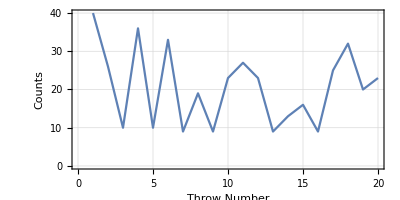
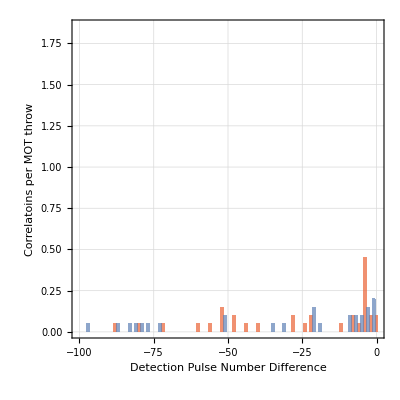
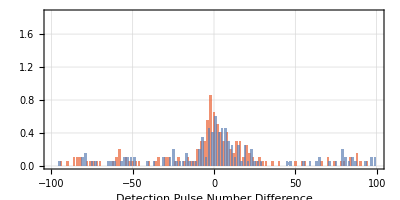
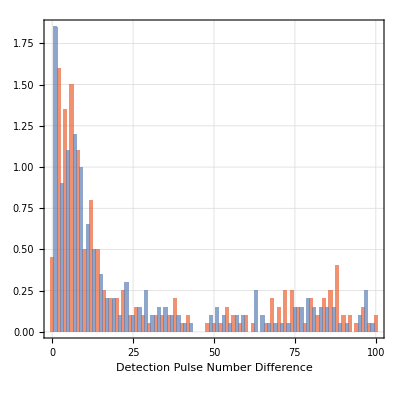
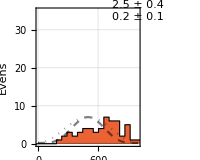
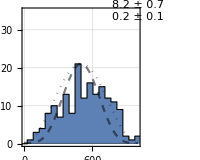
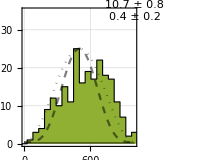
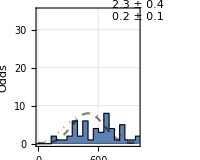
-Graphics- | -Graphics-
-Graphics--Graphics--Graphics- | 
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | Inset numbers of 'real' detections (background corrected) and background detections, per throw. | Interaction Time: | 30  ⟺  29.97 μs
 | 
Number MOT Throws: | 20
 | 
Real photons per throw: |     19.9    ±    1.0     
All Correlations per throw |     30.1    ±    1.7     
±1 Correlations per throw |     2.90    ±    0.40    
 | 
Atoms per throw: |     6.33    ±    0.75    
 Photon efficiency: |      0.1046  ±    0.0081

```mathematica
countCutOffs={1,200};
n=3;
atomWindow=Round[{5,21}10^3  / n];
backWindow=Round[{10,15}10^3];

detectors={0,1};
(*lag[0]=-330*^3;lag[1]=-330*^3;*)
photonLength=n*333*^3;
lag[0]=photonLength-400*^3;lag[1]=photonLength-400*^3;
tInter=30;

binLimit=100;(*Chose an even number*)
(*binWidth=1;*)

ANALYSIS[data1Raw]
```

### HOM - ±0 corrs

```mathematica
correlsHom=HomCorrelations[data3Windowed,{{0,1}}][[1]];
Length@correlsHom
N@Length[correlsHom]/Length[data3Windowed]
MinMax@correlsHom
```

5

0.0102881

{-281625,177777}

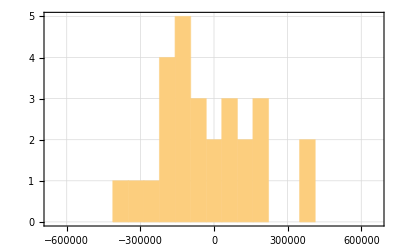

```mathematica
nbins=21;
HomHist = Histogram[correlsHom,{-photonLength,photonLength,2photonLength/nbins},genOpts]
```

### ±1 corrs

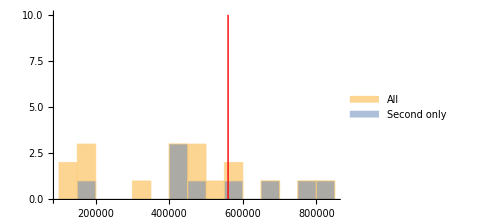
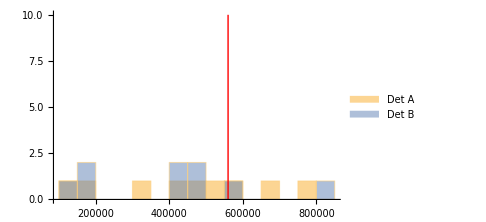
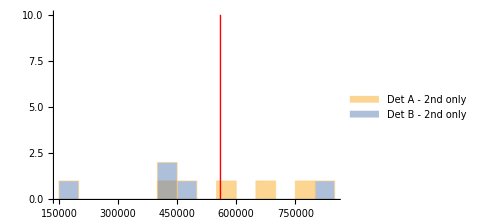
-Graphics- | -Graphics- | -Graphics-

```mathematica
dats=Flatten[(Transpose/@Transpose[{Outer[List,#[[1,;;,2]],#[[2,;;,2]]],Outer[Plus,#[[1,;;,4]],-#[[2,;;,4]]]}])&/@Transpose[FilterByDetector[data3Windowed,{0,1}]],2];

dets=Flatten[Select[dats,Abs[Last[#]]==1&][[;;,1]]];
detsDetAOnly=Select[dats,Abs[Last[#]]==1&][[;;,1,1]];
detsDetBOnly=Select[dats,Abs[Last[#]]==1&][[;;,1,2]];
detsDetASecondOnly=Select[dats,Last[#]==1&][[;;,1,1]];
detsDetBSecondOnly=Select[dats,Last[#]==-1&][[;;,1,2]];
detsSecondOnly=Join[detsDetASecondOnly,detsDetBSecondOnly];

lines = {560}*10^3;
ls = Graphics[{Red,Thick,Line[{{#,0},{#,10}}]}]&/@lines;

hist1 = Show[Histogram[{dets, detsSecondOnly},15,ChartLegends->{"All","Second only"},ImageSize->Medium],ls];
hist2 = Show[Histogram[{detsDetAOnly, detsDetBOnly},15,ChartLegends->{"Det A","Det B"},ImageSize->Medium],ls];
hist3=Show[ Histogram[{detsDetASecondOnly, detsDetBSecondOnly},15,ChartLegends->{"Det A - 2nd only","Det B - 2nd only"},ImageSize->Medium],ls];

Grid[{{hist1,hist2,hist3}}]
```

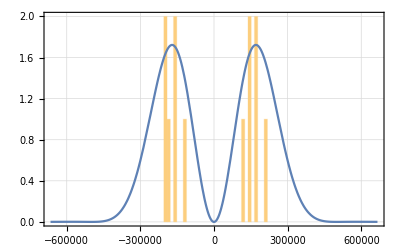

```mathematica
Δ=2*2Pi;
Lpulse = photonLength;
Lph = Lpulse * 700/832;
Show[HomHist,Plot[2(1-Cos[Δ*10^-6 t])ⅇ^((-2Pi t^2)/Lph^2),{t,-Lpulse,Lpulse}]]
```

### Detection Patterns

```mathematica
keys={{0},{1},{2},{0,0},{0,2},{2,0},{1,1},{2,2},{0,2,0},{2,0,2},{0,0,0}};
m=Max[keys]+1;
lens=Union[Length/@keys];


diffs=Developer`ToPackedArray/@(Differences/@data3Windowed[[;;,;;,4]]);
as=Join@@ParallelTable[
Counts[Pick[#,UnitStep[(Max/@#)-m],0]&@(Join@@(Partition[#,l,1]&/@diffs))],
{l,lens}
];

TableForm[{keys,as/@keys},TableDepth->2,TableAlignments->Center]
```

{0} | {1} | {2} | {0,0} | {0,2} | {2,0} | {1,1} | {2,2} | {0,2,0} | {2,0,2} | {0,0,0}
9 | 104 | 62 | Missing[KeyAbsent,{0,0}] | Missing[KeyAbsent,{0,2}] | Missing[KeyAbsent,{2,0}] | 4 | 3 | Missing[KeyAbsent,{0,2,0}] | Missing[KeyAbsent,{2,0,2}] | Missing[KeyAbsent,{0,0,0}]

```mathematica
correlsHom=HomCorrelations[data3Windowed,{{0,0},{0,2},{2,2}}];
Length[Flatten[correlsHom]]
```

70